```mathematica
Clear[x_k]
exes = {Cos[Pi/8],Cos[3*Pi/8],Cos[5*Pi/8],Cos[7*Pi/8]};
```

Clear::ssym: x_k is not a symbol or a string.

```mathematica
exes[[1]]
```

Cos[π/8]

```mathematica
lagrangePoly1[x_] = Expand[Product[N[(x-exes[[i]])/(exes[[1]]-exes[[i]])],{i,{2,3,4}}]]
lagrangePoly2[x_] = Expand[Product[N[(x-exes[[i]])/(exes[[2]]-exes[[i]])],{i,{1,3,4}}]]
lagrangePoly3[x_] = Expand[Product[N[(x-exes[[i]])/(exes[[3]]-exes[[i]])],{i,{1,2,4}}]]
lagrangePoly4[x_] = Expand[Product[N[(x-exes[[i]])/(exes[[4]]-exes[[i]])],{i,{1,2,3}}]]
```

-0.103553-0.112085 x+0.707107 x^2+0.765367 x^3

0.603553+1.57716 x-0.707107 x^2-1.84776 x^3

0.603553-1.57716 x-0.707107 x^2+1.84776 x^3

-0.103553+0.112085 x+0.707107 x^2-0.765367 x^3

```mathematica
polyList = {lagrangePoly1[x],lagrangePoly2[x],lagrangePoly3[x],lagrangePoly4[x]};
```

```mathematica
poly[x_]  = Expand[N[Sum[Exp[exes[[i]]]*polyList[[i]],{i,{1,2,3,4}}]]]
```

0.994615+0.998933 x+0.542901 x^2+0.175176 x^3

```mathematica
NSolve[{-x*(x+1)+2*y == 18, (x-1)^2 + (y-6)^2 ==25},{x,y},Reals]
```

{{x→-2.,y→10.},{x→1.54695,y→10.97}}

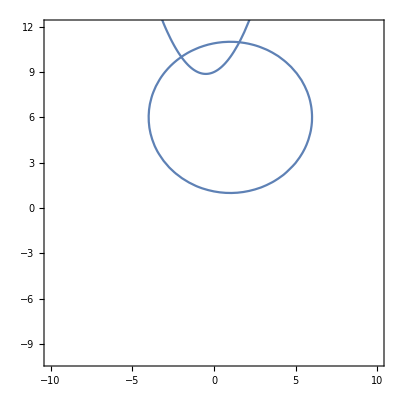

```mathematica
circle = ContourPlot[(x-1)^2+(y-6)^2==25,{x,-10,10},{y,-10,12}];
parabola = Plot[0.5*x*(x+1)+9,{x,-10,10}];
Show[circle, parabola]
```